```mathematica
(*Get the package for partially transposed permutation matrix algebra representation theory*)
Get[NotebookDirectory[]<>"walled_brauer_gt_basis.wl"]
```

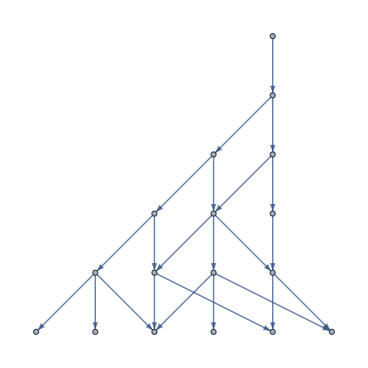

```mathematica
(*Set the parametrs for the algebra A*)
{p,q,d}={3,2,3};

(*Draw Bratteli diagram *)
SetProperty[BratteliDiagram[p,q,d],{EdgeLabels->Placed["Name",Tooltip,#[[All,1;;2]]&],VertexLabels->Placed["Name",Tooltip,#[[1;;2]]&]}]
```

```mathematica
(*Display the dimensions of the irreps and display all mixed Young tableaux for every irrep*)
IrrepDims[p,q,d]
DisplayAllPathsAsYT[AllPaths[p,q,d]]//TableForm
```

{1,1,2,6,5,6}

1 | 2 | 3
4 | 5 |  |  |  |  | 
1 | 2 | 3
4
5 |  |  |  |  | 
1 | 3
2 | 
4 | 5 | 1 | 2
3 | 
4 | 5 |  |  |  | 
1 | 3
2,4 | 
5 | 1 | 3
2,5 | 
4 | 1 | 2
3,4 | 
5 | 1 | 2
3,5 | 
4 | 1 | 2 | 3,4
5 | 1 | 2 | 3,5
4
1
2
3,4
5 | 1 | 3,4
2 | 
5 | 1 | 3,5
2 | 
4 | 1 | 2,4
3 | 
5 | 1 | 2,5
3 | 
4 | 
1
2,5
3,4
∅ | 1 | 3,4
2,5 | 
∅ | 1 | 3,5
2,4 | 
∅ | 1 | 2,4
3,5 | 
∅ | 1 | 2,5
3,4 | 
∅ | 1 | 2,5 | 3,4
∅

```mathematica
(*Compute all generators' matrices for each irrep*)
allGenMatrices=AllGeneratorsGT[p,q,d];

(*Show all generators' irrep matrices: each row corresponds to different generators Subscript[σ, i] and each column - to different irreps*)
TableForm[(MatrixForm/@#)&/@allGenMatrices]
```

(1) | (1) | (-1 | 0
0 | 1) | (-1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1) | (-1 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1) | (-1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)
(1) | (1) | (1/2 | (√3)/2
(√3)/2 | -1/2) | (1/2 | 0 | (√3)/2 | 0 | 0 | 0
0 | 1/2 | 0 | (√3)/2 | 0 | 0
(√3)/2 | 0 | -1/2 | 0 | 0 | 0
0 | (√3)/2 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1) | (-1 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | (√3)/2 | 0
0 | 0 | 1/2 | 0 | (√3)/2
0 | (√3)/2 | 0 | -1/2 | 0
0 | 0 | (√3)/2 | 0 | -1/2) | (-1 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | (√3)/2 | 0 | 0
0 | 0 | 1/2 | 0 | (√3)/2 | 0
0 | (√3)/2 | 0 | -1/2 | 0 | 0
0 | 0 | (√3)/2 | 0 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 1)
(0) | (0) | (0 | 0
0 | 0) | (0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4/3 | 0 | (2 √5)/3 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (2 √5)/3 | 0 | 5/3 | 0
0 | 0 | 0 | 0 | 0 | 0) | (1/3 | (2 √2)/3 | 0 | 0 | 0
(2 √2)/3 | 8/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (1/3 | (2 √2)/3 | 0 | 0 | 0 | 0
(2 √2)/3 | 8/3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4/3 | (2 √5)/3
0 | 0 | 0 | 0 | (2 √5)/3 | 5/3)
(1) | (-1) | (1 | 0
0 | 1) | (1/2 | (√3)/2 | 0 | 0 | 0 | 0
(√3)/2 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | (√3)/2 | 0 | 0
0 | 0 | (√3)/2 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | 1/5 | (2 √6)/5
0 | 0 | 0 | 0 | (2 √6)/5 | -1/5) | (1 | 0 | 0 | 0 | 0
0 | 1/4 | (√15)/4 | 0 | 0
0 | (√15)/4 | -1/4 | 0 | 0
0 | 0 | 0 | 1/4 | (√15)/4
0 | 0 | 0 | (√15)/4 | -1/4) | (-1 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | (√3)/2 | 0 | 0 | 0
0 | (√3)/2 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | (√3)/2 | 0
0 | 0 | 0 | (√3)/2 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(*Check all algebra relations (shows "True" if they are satisfied) and show them if they are not satisfied *)
Table[CheckRelations[allGenMatrices[[All,λ]],p,q,d],{λ,Length@IrrepDims[p,q,d]}]//MatrixForm;
If[And@@Flatten@Table[CheckRelations[allGenMatrices[[All,λ]],p,q,d],{λ,Length@IrrepDims[p,q,d]}],True,%]
```

True